### Solow growth

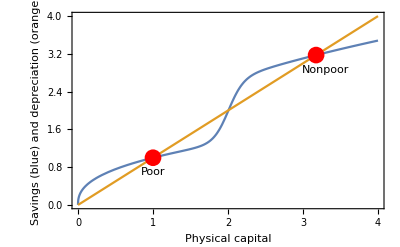

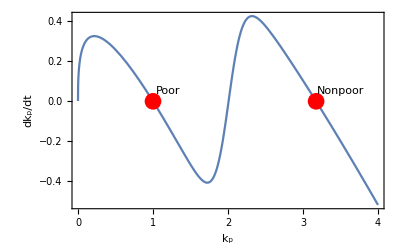

```mathematica
A=10;
α1=Rationalize[0.4];
s1=Rationalize[0.1];
s2=Rationalize[0.2];
s3=10;
d=2;
δP=Rationalize[0.5];
n=Rationalize[0.5];

f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
Savings:=sf[kP] f[kP]
Depreciation:=(δP+n) kP

data:={{1.00008,1.00008},{3.174781185869739,3.174781185869739}};
p1=Plot[{Savings,Depreciation}, {kP,0,4}, 
Frame->True, FrameLabel->{"Physical capital", "Savings (blue) and depreciation (orange)"}];
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
p3=Graphics[{Text[Poor,{1,0.7}],Text[Nonpoor,{3.3,2.85}]}];
Show[{p1,p2,p3}]

data:={{1.00008,0},{3.174781185869739,0}};
p1=Plot[Savings-Depreciation,{kP,0,4},
Frame->True, FrameLabel->{"k_p", "dk_p/dt"}];
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
p3=Graphics[{Text[Poor,{1.2,0.05}],Text[Nonpoor,{3.5,0.05}]}];
Show[{p1,p2,p3}]
```

Double well potential energy U(x)

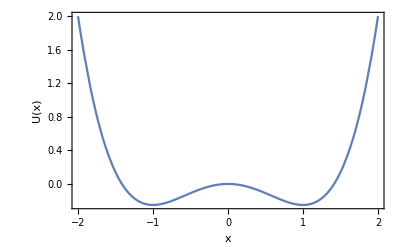

```mathematica
U[x_]:=x^4/4-x^2/2;
Plot[U[x], {x,-2,2},Frame->True, FrameLabel->{"x", "U(x)"},Axes->False]
```

### Deterministic Langevin dynamics

U(x)=1/4x^4-1/2x^2
Only deterministic part Langevin dynamics (so without noise):
dx/dt = -dU/dx = -(x^3-x) = -x^3+x

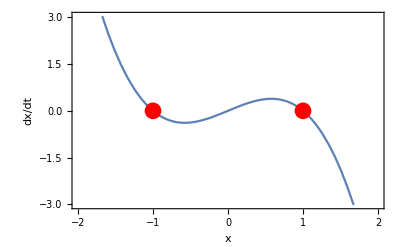

```mathematica
p1=Plot[-U'[x], {x,-2,2},Frame->True, FrameLabel->{"x","dx/dt"}];
data:={{-1,0},{1,0}};
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
Show[{p1,p2}]
```

Red points are equilibrium points.

### Stochastic Langevin Dynamics

#### Additive noise

See Figure 2 in paper Shaping the Epigenetic Landscape: Complexities and Consequences

2.92484×10^-7

0.0239801

0.240209

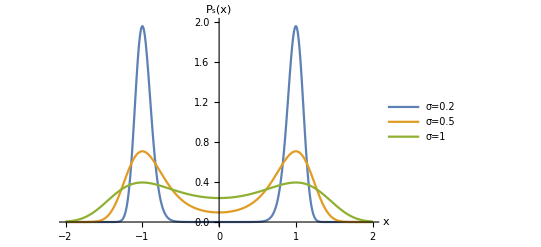

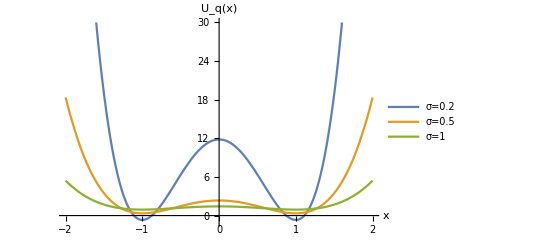

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
g[x_,σ_]:=σ;
α=0; (* ito *)
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;
Ps[x_,σ_,N_]:=N/σ^2 Exp[-2/σ^2 U[x]];  (* eq 9 *)
Uq[x_,σ_,N_]:=2U[x]/σ^2+Log[σ^2/N]; (* eq 10 *)
(* Uq2[x_,σ_,N_]:=-Log[N/σ^2Exp[-2/σ^2U[x]]]; *)

σ=σlow=0.2;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nlow=N/.Nvalue[[1]];
Print[Nlow]

σ=σmid=0.5;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area2=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area2==1,N];
Nmid=N/.Nvalue[[1]];
Print[Nmid]

σ=σhigh=1;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area3=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area3==1,N];
Nhigh=N/.Nvalue[[1]];
Print[Nhigh]

Plot[{Evaluate[Ps[x,σlow,Nlow]],Evaluate[Ps[x,σmid,Nmid]],Evaluate[Ps[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{0,2},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
Plot[{Evaluate[Uq[x,σlow,Nlow]],Evaluate[Uq[x,σmid,Nmid]],Evaluate[Uq[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,30},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
(* Plot[{Evaluate[Uq2[x,σlow,Nlow]],Evaluate[Uq2[x,σmid,Nmid]],Evaluate[Uq2[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,30},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}] *)
```

#### Multiplicative noise

Example 1: Shifting the fixed points
See Figure 3 in paper

2.40164×10^-39

-0.439111

2.41824×10^-7

0.0205906

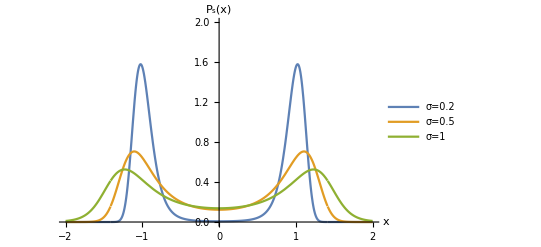

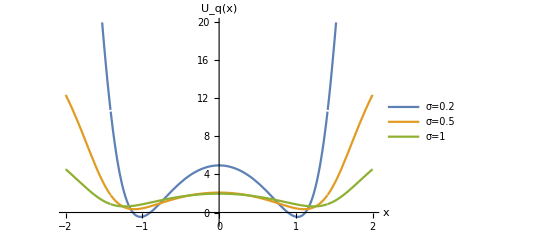

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
g[x_,σ_]:=σ/4(x^4-4 x^2+8);
α=0; (* ito *)
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;
(* IntegrationConstant[σ_]=1/σ^2(ArcTan[1]+3/2)+2 α Log[8]; *)
IntegrationConstant[σ_]=1;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Ps[x_,σ_,N_]:=16 N/σ^2 Exp[2(α-1)Log[x^4-4 x^2+8]+1/σ^2(ArcTan[1-x^2/2]-2(x^2-6)/(x^4-4 x^2+8)+IntegrationConstant[σ])]; (* eq 11 *)
(* Uq[x_,σ_,N_]:=Log[σ^2/(16 N) (x^4-x^2+8)^(2(1-α))]-1/σ^2(ArcTan[1-x^2/2]-(2 (x^2-6))/(x^4-x^2+8))-IntegrationConstant[σ]; *) (* eq 12 *)
Uq[x_,σ_,N_]:=-Log[16 N/σ^2 Exp[2(α-1)Log[x^4-4 x^2+8]+1/σ^2(ArcTan[1-x^2/2]-2(x^2-6)/(x^4-4 x^2+8)+IntegrationConstant[σ])]];

σ=σlow=0.2;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area1=Sum[TrapezoidalRulePs[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nlow=N/.Nvalue[[1]];
Print[Nlow]
Print[Uq[1,σlow,Nlow]]

σ=σmid=0.5;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area2=Sum[TrapezoidalRulePs[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area2==1,N];
Nmid=N/.Nvalue[[1]];
Print[Nmid]

σ=σhigh=1;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area3=Sum[TrapezoidalRulePs[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area3==1,N];
Nhigh=N/.Nvalue[[1]];
Print[Nhigh]

Plot[{Evaluate[Ps[x,σlow,Nlow]],Evaluate[Ps[x,σmid,Nmid]],Evaluate[Ps[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{0,2},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
Plot[{Evaluate[Uq[x,σlow,Nlow]],Evaluate[Uq[x,σmid,Nmid]],Evaluate[Uq[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,20},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
```

Example 2: Creation and destruction of fixed points
See Figure 4 in paper

0.0000691993

0.0864627

0.573664

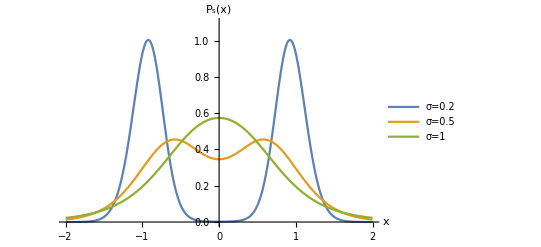

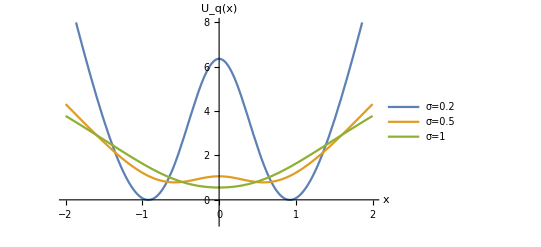

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
g[x_,σ_]:=σ(1+x^2);
α=0; (* ito *)
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;
IntegrationConstant[σ_]:=2;
Ps[x_,σ_,N_]:=N/(σ^2(1+x^2)^2)Exp[1/σ^2((2 α σ^2-1)Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ])]; (* eq 13 *)
Uq[x_,σ_,N_]:=Log[σ^2 (1+x^2)^2/N]-1/σ^2 ((2 α σ^2-1) Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ]); (* eq 14 *)

σ=σlow=0.2;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nlow=N/.Nvalue[[1]];
Print[Nlow]

σ=σmid=0.5;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area2=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area2==1,N];
Nmid=N/.Nvalue[[1]];
Print[Nmid]

σ=σhigh=1;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area3=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area3==1,N];
Nhigh=N/.Nvalue[[1]];
Print[Nhigh]

Plot[{Evaluate[Ps[x,σlow,Nlow]],Evaluate[Ps[x,σmid,Nmid]],Evaluate[Ps[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{0,1.1},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
Plot[{Evaluate[Uq[x,σlow,Nlow]],Evaluate[Uq[x,σmid,Nmid]],Evaluate[Uq[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,8},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
```

Figure 5 in paper

0.23862

0.154879

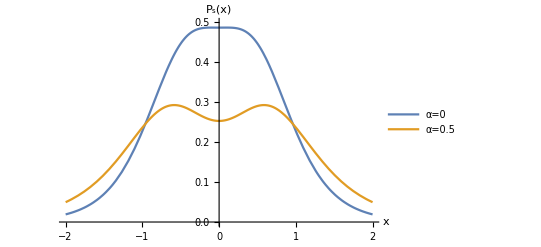

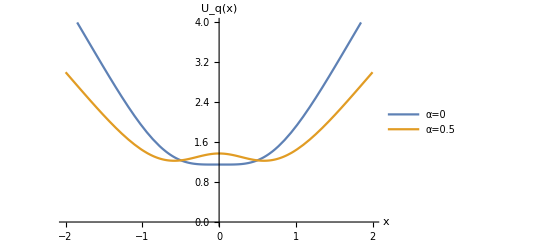

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
σ=0.7;
g[x_,σ_]:=σ(1+x^2);
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;
IntegrationConstant[σ_]:=2;
Ps[x_,σ_,α_,N_]:=N/(σ^2(1+x^2)^2)Exp[1/σ^2((2 α σ^2-1)Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ])]; (* eq 13 *)
Uq[x_,σ_,α_,N_]:=Log[σ^2 (1+x^2)^2/N]-1/σ^2 ((2 α σ^2-1) Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ]); (* eq 14 *)

α=αito=0; (* ito *)
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,αito,N]+Ps[b,σ,αito,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nito=N/.Nvalue[[1]];
Print[Nito]

α=αstra=0.5; 
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,αstra,N]+Ps[b,σ,αstra,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nstra=N/.Nvalue[[1]];
Print[Nstra]

Plot[{Evaluate[Ps[x,σ,αito,Nito]],Evaluate[Ps[x,αstra,Nc]]},{x,-2,2},PlotRange->{0,0.5},AxesLabel->{"x","P_s(x)"},PlotLegends->{"α=0","α=0.5"}]
Plot[{Evaluate[Uq[x,σ,αito,Nstra]],Evaluate[Uq[x,αstra,Nc]]},{x,-2,2},PlotRange->{0,4},AxesLabel->{"x","U_q(x)"},PlotLegends->{"α=0","α=0.5"}]
```